```mathematica
WavepacketA=Exp[-Γ t]Exp[(-(x+c t)^2)/(2 σ^2)]Sin[k0 x+ k0 c t];
WavepacketB=Exp[-Γ t]Exp[(-(x-c t)^2)/(2 σ^2)]Sin[k0 x- k0 c t];
```

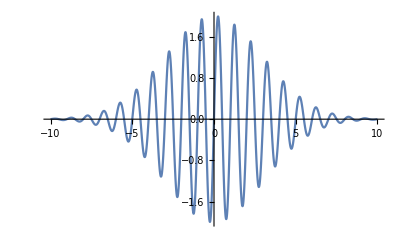

```mathematica
Plot[WavepacketA+WavepacketB/.{k0->2 π,Γ->0,t->0,c->1,σ->3},{x,-10,10},PlotRange->All]
```

```mathematica
DensityPlot[WavepacketA+WavepacketB/.{k0->2 π,Γ->0.3,c->1,σ->1},{x,-10,10},{t,0,10},PlotRange->{-1.5,1.5},ColorFunction->"RedGreenSplit",PlotPoints->100]
```

-Graphics-

```mathematica
DensityPlot[WavepacketA+WavepacketB/.{k0->2 π,Γ->0.3,c->1,σ->5},{x,-10,10},{t,0,10},PlotRange->{-1.5,1.5},ColorFunction->"RedGreenSplit",PlotPoints->100]
```

-Graphics-

```mathematica
ft=FourierTransform[WavepacketA+WavepacketB,x,k]//FullSimplify
```

(ⅈ ⅇ^(-ⅈ c k t-t Γ-1/2 (k+k0)^2 σ^2) (1+ⅇ^(2 ⅈ c k t)) (-1+ⅇ^(2 k k0 σ^2)))/(2 √(1/σ^2))

```mathematica
ps=FullSimplify[Abs[ft]^2,c>0&&Γ>0&&k0>0&&σ>0&&t>0&&k>0]
```

ⅇ^(-2 t Γ-(k+k0)^2 σ^2) (-1+ⅇ^(2 k k0 σ^2))^2 σ^2 Cos[c k t]^2

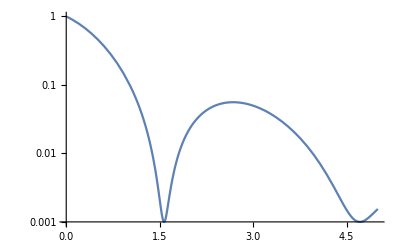

```mathematica
psoft=Exp[-t Γ]Cos[ω t]^2;
LogPlot[psoft+.001/.{Γ->1,ω->1},{t,0,5}]
```